## Functions

```mathematica
ReplaceDiagonal[m_]:=Module[{mat=m},Scan[(mat[[Sequence@@#]]=0)&,Table[{i,i},{i,Length@m}]];mat];
originalColorsValues={{70,50,0,0},{0,100,0,0},{0,0,0,0},{100,100,100,100},{0,0,0,0}};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
MapProcess[freqs_, pops_, latLon_,max_,countryName_,surv_,over_]:=Module[{
scA=10000,scB=35000, scC=.0015, cA="#1e59fc", cB="#ff007f",cC="#7737d6"
},
GeoGraphics[{
GeoStyling[EdgeForm[Directive[Opacity[.1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[0],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[0],Thickness[.1],colorPalette[[5]]]],Opacity[0],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.1],Thickness[.02],hexToRGB["#356afc"]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->Automatic
,Axes->False
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->Black
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Opacity[.25],Thickness[.001],Black}]
,ImageSize->1500
,GeoBackground->None
(*,GeoBackground->GeoStyling["ReliefMap"]
,GeoServer->"DigitalGlobe"*)
,PlotRange->{{6.6,6.75},{0.25,.4}}
,Epilog->{
(*Centrality*)
Lighter[hexToRGB[cA],.25],Opacity[.25],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cA]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@latLon,(scA*(pops/Max[pops]/scB)*(freqs/max/scB))^(1/2)}],
(*Surveillance*)
hexToRGB[cB],Opacity[0.2],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cB]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@(latLon[[#]]&/@surv),(scA*((pops[[#]]&/@surv)/Max[pops]/scB)*((freqs[[#]]&/@surv)/max/scB))^(1/2)}],
(*Overrun*)
hexToRGB[cB],Opacity[0.1],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cC]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@(latLon[[#]]&/@over),(scA*((pops[[#]]&/@over)/Max[pops]/scB)*((freqs[[#]]&/@over)/max/scB))^(1/2)}],
(*PopSize*)
Darker[hexToRGB[cA],0],Opacity[0],EdgeForm[Directive[Thickness[.003],Dashing[.0025],Opacity[.05],Darker[hexToRGB[cA],.1]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@latLon,(pops/Max[pops]/scB)^(1/2)}]
}
]
];
HistProcess[steps_,migration_,max_]:=Module[{},
Histogram[steps,migration//Length
,AspectRatio->.1
,Axes->False
,ChartStyle->Directive[{EdgeForm[Directive[{hexToRGB["#80A1FC"],Opacity[0],Thick}]],Opacity[.5],hexToRGB["#80A1FC"]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,ImageSize->1500
,PlotRange->{{0,migration//Length},{0,max}}
]
]
```

## Load Data

```mathematica
SetDirectory[NotebookDirectory[]];
bPath= "./kernels_cluster/";
lonLatPop=Import[bPath<>"stp_cluster_sites_pop.csv"][[2;;All]];
migration=Import[bPath<>"kernel_cluster_2500_2.csv"];
(**)
latLon=Reverse/@lonLatPop[[All,1;;2]];
pops=Log[lonLatPop[[All,3]]]//N;
```

## Markov Process

```mathematica
{sp,rep}={500,10000};
(*Simulate*)
initialState=ConstantArray[0,migration//Length]//ReplacePart[#,258->1]&;
markov=DiscreteMarkovProcess[initialState,migration];
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
simTraces=(RandomFunction[markov,{0,sp},rep]//Normal);
steps=#[[All,2]]&/@simTraces;
{max,maxTwo}={Tally[steps//Flatten][[All,2]]//Max,Tally[steps//Flatten][[All,2]]//Max};
```

## Export Ring

```mathematica
Table[
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(*surv=Position[freqs,#]&/@topFreq//Flatten;*)
over=Position[freqs,x_/;1500≤x]//Flatten;
surv=Position[freqs,x_/;300<x<1500]//Flatten;
(*Map*)
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
out=map;(*Grid[{{hst},{map}}];*)
(**)
Export["./img/map"<>StringPadLeft[t//ToString,4,"0"]<>".png",out]
,{t,sp}]
```

{./img/map0001.png,./img/map0002.png,./img/map0003.png,./img/map0004.png,./img/map0005.png,./img/map0006.png,./img/map0007.png,./img/map0008.png,./img/map0009.png,./img/map0010.png,./img/map0011.png,./img/map0012.png,./img/map0013.png,./img/map0014.png,./img/map0015.png,./img/map0016.png,./img/map0017.png,./img/map0018.png,./img/map0019.png,./img/map0020.png,./img/map0021.png,./img/map0022.png,./img/map0023.png,./img/map0024.png,./img/map0025.png,./img/map0026.png,./img/map0027.png,./img/map0028.png,./img/map0029.png,./img/map0030.png,./img/map0031.png,./img/map0032.png,./img/map0033.png,./img/map0034.png,./img/map0035.png,./img/map0036.png,./img/map0037.png,./img/map0038.png,./img/map0039.png,./img/map0040.png,./img/map0041.png,./img/map0042.png,./img/map0043.png,./img/map0044.png,./img/map0045.png,./img/map0046.png,./img/map0047.png,./img/map0048.png,./img/map0049.png,./img/map0050.png,./img/map0051.png,./img/map0052.png,./img/map0053.png,./img/map0054.png,./img/map0055.png,./img/map0056.png,./img/map0057.png,./img/map0058.png,./img/map0059.png,./img/map0060.png,./img/map0061.png,./img/map0062.png,./img/map0063.png,./img/map0064.png,./img/map0065.png,./img/map0066.png,./img/map0067.png,./img/map0068.png,./img/map0069.png,./img/map0070.png,./img/map0071.png,./img/map0072.png,./img/map0073.png,./img/map0074.png,./img/map0075.png,./img/map0076.png,./img/map0077.png,./img/map0078.png,./img/map0079.png,./img/map0080.png,./img/map0081.png,./img/map0082.png,./img/map0083.png,./img/map0084.png,./img/map0085.png,./img/map0086.png,./img/map0087.png,./img/map0088.png,./img/map0089.png,./img/map0090.png,./img/map0091.png,./img/map0092.png,./img/map0093.png,./img/map0094.png,./img/map0095.png,./img/map0096.png,./img/map0097.png,./img/map0098.png,./img/map0099.png,./img/map0100.png,./img/map0101.png,./img/map0102.png,./img/map0103.png,./img/map0104.png,./img/map0105.png,./img/map0106.png,./img/map0107.png,./img/map0108.png,./img/map0109.png,./img/map0110.png,./img/map0111.png,./img/map0112.png,./img/map0113.png,./img/map0114.png,./img/map0115.png,./img/map0116.png,./img/map0117.png,./img/map0118.png,./img/map0119.png,./img/map0120.png,./img/map0121.png,./img/map0122.png,./img/map0123.png,./img/map0124.png,./img/map0125.png,./img/map0126.png,./img/map0127.png,./img/map0128.png,./img/map0129.png,./img/map0130.png,./img/map0131.png,./img/map0132.png,./img/map0133.png,./img/map0134.png,./img/map0135.png,./img/map0136.png,./img/map0137.png,./img/map0138.png,./img/map0139.png,./img/map0140.png,./img/map0141.png,./img/map0142.png,./img/map0143.png,./img/map0144.png,./img/map0145.png,./img/map0146.png,./img/map0147.png,./img/map0148.png,./img/map0149.png,./img/map0150.png,./img/map0151.png,./img/map0152.png,./img/map0153.png,./img/map0154.png,./img/map0155.png,./img/map0156.png,./img/map0157.png,./img/map0158.png,./img/map0159.png,./img/map0160.png,./img/map0161.png,./img/map0162.png,./img/map0163.png,./img/map0164.png,./img/map0165.png,./img/map0166.png,./img/map0167.png,./img/map0168.png,./img/map0169.png,./img/map0170.png,./img/map0171.png,./img/map0172.png,./img/map0173.png,./img/map0174.png,./img/map0175.png,./img/map0176.png,./img/map0177.png,./img/map0178.png,./img/map0179.png,./img/map0180.png,./img/map0181.png,./img/map0182.png,./img/map0183.png,./img/map0184.png,./img/map0185.png,./img/map0186.png,./img/map0187.png,./img/map0188.png,./img/map0189.png,./img/map0190.png,./img/map0191.png,./img/map0192.png,./img/map0193.png,./img/map0194.png,./img/map0195.png,./img/map0196.png,./img/map0197.png,./img/map0198.png,./img/map0199.png,./img/map0200.png,./img/map0201.png,./img/map0202.png,./img/map0203.png,./img/map0204.png,./img/map0205.png,./img/map0206.png,./img/map0207.png,./img/map0208.png,./img/map0209.png,./img/map0210.png,./img/map0211.png,./img/map0212.png,./img/map0213.png,./img/map0214.png,./img/map0215.png,./img/map0216.png,./img/map0217.png,./img/map0218.png,./img/map0219.png,./img/map0220.png,./img/map0221.png,./img/map0222.png,./img/map0223.png,./img/map0224.png,./img/map0225.png,./img/map0226.png,./img/map0227.png,./img/map0228.png,./img/map0229.png,./img/map0230.png,./img/map0231.png,./img/map0232.png,./img/map0233.png,./img/map0234.png,./img/map0235.png,./img/map0236.png,./img/map0237.png,./img/map0238.png,./img/map0239.png,./img/map0240.png,./img/map0241.png,./img/map0242.png,./img/map0243.png,./img/map0244.png,./img/map0245.png,./img/map0246.png,./img/map0247.png,./img/map0248.png,./img/map0249.png,./img/map0250.png,./img/map0251.png,./img/map0252.png,./img/map0253.png,./img/map0254.png,./img/map0255.png,./img/map0256.png,./img/map0257.png,./img/map0258.png,./img/map0259.png,./img/map0260.png,./img/map0261.png,./img/map0262.png,./img/map0263.png,./img/map0264.png,./img/map0265.png,./img/map0266.png,./img/map0267.png,./img/map0268.png,./img/map0269.png,./img/map0270.png,./img/map0271.png,./img/map0272.png,./img/map0273.png,./img/map0274.png,./img/map0275.png,./img/map0276.png,./img/map0277.png,./img/map0278.png,./img/map0279.png,./img/map0280.png,./img/map0281.png,./img/map0282.png,./img/map0283.png,./img/map0284.png,./img/map0285.png,./img/map0286.png,./img/map0287.png,./img/map0288.png,./img/map0289.png,./img/map0290.png,./img/map0291.png,./img/map0292.png,./img/map0293.png,./img/map0294.png,./img/map0295.png,./img/map0296.png,./img/map0297.png,./img/map0298.png,./img/map0299.png,./img/map0300.png,./img/map0301.png,./img/map0302.png,./img/map0303.png,./img/map0304.png,./img/map0305.png,./img/map0306.png,./img/map0307.png,./img/map0308.png,./img/map0309.png,./img/map0310.png,./img/map0311.png,./img/map0312.png,./img/map0313.png,./img/map0314.png,./img/map0315.png,./img/map0316.png,./img/map0317.png,./img/map0318.png,./img/map0319.png,./img/map0320.png,./img/map0321.png,./img/map0322.png,./img/map0323.png,./img/map0324.png,./img/map0325.png,./img/map0326.png,./img/map0327.png,./img/map0328.png,./img/map0329.png,./img/map0330.png,./img/map0331.png,./img/map0332.png,./img/map0333.png,./img/map0334.png,./img/map0335.png,./img/map0336.png,./img/map0337.png,./img/map0338.png,./img/map0339.png,./img/map0340.png,./img/map0341.png,./img/map0342.png,./img/map0343.png,./img/map0344.png,./img/map0345.png,./img/map0346.png,./img/map0347.png,./img/map0348.png,./img/map0349.png,./img/map0350.png,./img/map0351.png,./img/map0352.png,./img/map0353.png,./img/map0354.png,./img/map0355.png,./img/map0356.png,./img/map0357.png,./img/map0358.png,./img/map0359.png,./img/map0360.png,./img/map0361.png,./img/map0362.png,./img/map0363.png,./img/map0364.png,./img/map0365.png,./img/map0366.png,./img/map0367.png,./img/map0368.png,./img/map0369.png,./img/map0370.png,./img/map0371.png,./img/map0372.png,./img/map0373.png,./img/map0374.png,./img/map0375.png,./img/map0376.png,./img/map0377.png,./img/map0378.png,./img/map0379.png,./img/map0380.png,./img/map0381.png,./img/map0382.png,./img/map0383.png,./img/map0384.png,./img/map0385.png,./img/map0386.png,./img/map0387.png,./img/map0388.png,./img/map0389.png,./img/map0390.png,./img/map0391.png,./img/map0392.png,./img/map0393.png,./img/map0394.png,./img/map0395.png,./img/map0396.png,./img/map0397.png,./img/map0398.png,./img/map0399.png,./img/map0400.png,./img/map0401.png,./img/map0402.png,./img/map0403.png,./img/map0404.png,./img/map0405.png,./img/map0406.png,./img/map0407.png,./img/map0408.png,./img/map0409.png,./img/map0410.png,./img/map0411.png,./img/map0412.png,./img/map0413.png,./img/map0414.png,./img/map0415.png,./img/map0416.png,./img/map0417.png,./img/map0418.png,./img/map0419.png,./img/map0420.png,./img/map0421.png,./img/map0422.png,./img/map0423.png,./img/map0424.png,./img/map0425.png,./img/map0426.png,./img/map0427.png,./img/map0428.png,./img/map0429.png,./img/map0430.png,./img/map0431.png,./img/map0432.png,./img/map0433.png,./img/map0434.png,./img/map0435.png,./img/map0436.png,./img/map0437.png,./img/map0438.png,./img/map0439.png,./img/map0440.png,./img/map0441.png,./img/map0442.png,./img/map0443.png,./img/map0444.png,./img/map0445.png,./img/map0446.png,./img/map0447.png,./img/map0448.png,./img/map0449.png,./img/map0450.png,./img/map0451.png,./img/map0452.png,./img/map0453.png,./img/map0454.png,./img/map0455.png,./img/map0456.png,./img/map0457.png,./img/map0458.png,./img/map0459.png,./img/map0460.png,./img/map0461.png,./img/map0462.png,./img/map0463.png,./img/map0464.png,./img/map0465.png,./img/map0466.png,./img/map0467.png,./img/map0468.png,./img/map0469.png,./img/map0470.png,./img/map0471.png,./img/map0472.png,./img/map0473.png,./img/map0474.png,./img/map0475.png,./img/map0476.png,./img/map0477.png,./img/map0478.png,./img/map0479.png,./img/map0480.png,./img/map0481.png,./img/map0482.png,./img/map0483.png,./img/map0484.png,./img/map0485.png,./img/map0486.png,./img/map0487.png,./img/map0488.png,./img/map0489.png,./img/map0490.png,./img/map0491.png,./img/map0492.png,./img/map0493.png,./img/map0494.png,./img/map0495.png,./img/map0496.png,./img/map0497.png,./img/map0498.png,./img/map0499.png,./img/map0500.png}

## Export Static

```mathematica
{tts,sites}={120,20};
Table[
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(**)
freqsB=Count[steps[[All,1;;tts]]//Flatten,#]&/@Range[1,Length[migration]];
topFreqB=(freqs//Sort//Reverse)[[1;;sites]];
surv=Position[freqsB,x_/;750<x<1500]//Flatten;
(*Map*);
over=Position[freqs,x_/;1500<x]//Flatten;
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
out=map(*Grid[{{hst},{map}}];*);
(**)
Export["./img/map"<>StringPadLeft[t//ToString,4,"0"]<>".png",out]
,{t,sp}]
```

$Aborted

{62,69,102,110,164,165,166,168,169,170,200,202,204,206,207,209,244,246,247,249,250,252,254}

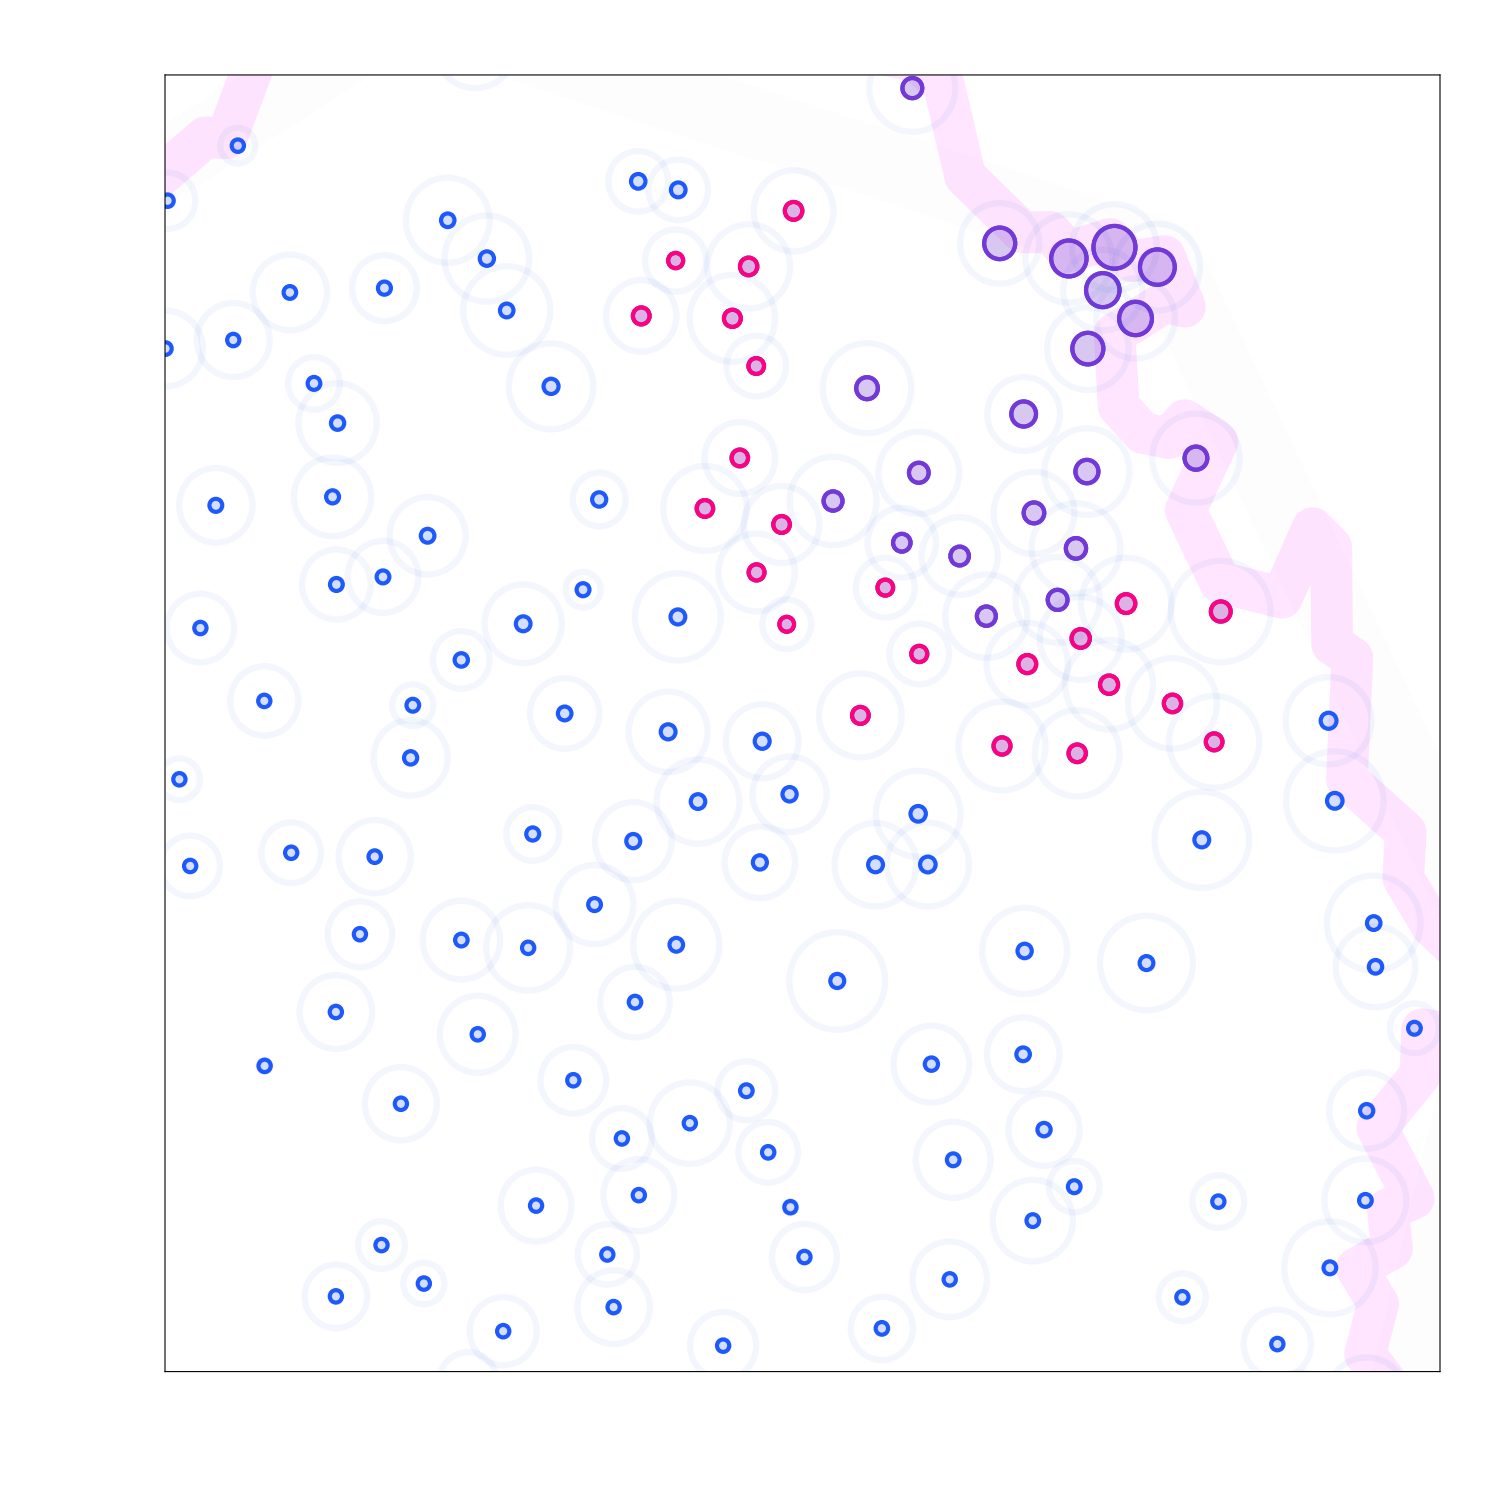

```mathematica
t=100;
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(*surv=Position[freqs,#]&/@topFreq//Flatten;*)
over=Position[freqs,x_/;1500<x]//Flatten;
surv=Position[freqs,x_/;500<x<1500]//Flatten;
(*Map*)
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
surv
out=map(*Grid[{{hst},{map}}];*)
```

## Tests

```mathematica
MatrixPlot[ReplaceDiagonal[migration]
,ColorFunction->Automatic
,ColorFunctionScaling->True
,FrameStyle->Thick
,FrameTicks->None
,ImagePadding->0
];
```